5.8

2.52

-0.20945

0.0804

0.394

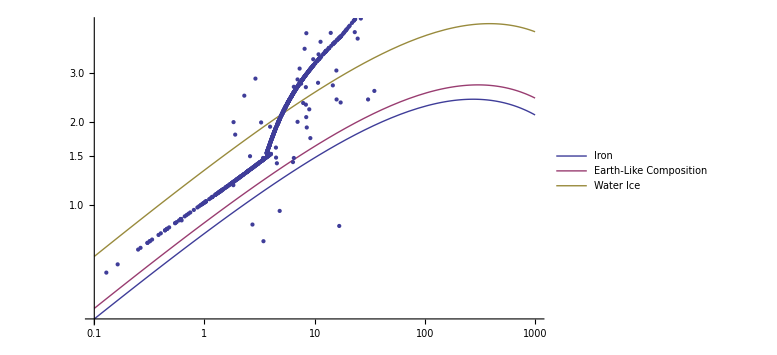

```mathematica
m1=5.80
r1=2.52
k1=-.20945
k2=.0804
k3=.394
R[M_,m1_,r1_,k1_,k2_,k3_]:=r1*10^(k1+1/3*Log10[M/m1]-k2*(M/m1)^k3)
Show[
LogLogPlot[{R[M,5.80,2.52,-.20945,.0804,.394],
R[M,6.41,2.84,-.20945,.0804,.394],
R[M,8.16,4.73,-.20945,.0804,.394]}
,{M,.1,1000},PlotLegends->{"Iron", "Earth-Like Composition", "Water Ice"}]
,
ListLogLogPlot[Import["/Users/rvilim/Documents/Research/Thesis/Chapter5/Figures/ExoplanetMass/MassRadius.csv"]]
]
```

```mathematica
P0[Z_]:=9.52*10^13*Z^(10/3)
R0[Z_,A_]:=Z/A*Z^(-1/3)*9.73*10^9
M0[Z_,A_]:=(Z/A)^2*Z*3.58*10^30
phi[Z_]:=3^(1/3)/20+1/8*(3/4*π^-2*Z^-2)^(1/3)
beta[Z_]:=3.562+5.634*Z^(-1/2)
alpha[Z_]:=beta[Z]^(5/3)/.4242


maxmass=10^31
nummass=2
Table[
Select[
R/.NSolve[((M/M0[Z,A])^(1/3)*R/R0[Z,A]==alpha[Z]/beta[Z]^(5/3)*(1-((R^3*M0[Z,A])/(R0[Z,A]^3*M))^(1/3)phi[Z])^5)/.A->1/.Z->1,R]
,Im@#==0&]
,{M,1,maxmass,maxmass/nummass}]
```

10000000000000000000000000000000

2

{{5.08795},{1.06669×10^10}}

```mathematica
Select[
R/.NSolve[((M/M0[Z,A])^(1/3)*R/R0[Z,A]==alpha[Z]/beta[Z]^(5/3)*(1-((R^3*M0[Z,A])/(R0[Z,A]^3*M))^(1/3)phi[Z])^5)/.A->1/.Z->1/.M->10,R]
,Im@#==0&]
```

{10.9558}